```mathematica
SetDirectory["C:\\anaconda32\\Work\\OnlineModel\\SimulationFramework\\Examples\\transverse_DCP_best_Short_240"]
```

C:\anaconda32\Work\OnlineModel\SimulationFramework\Examples\transverse_DCP_best_Short_240

```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\SimulationFramework\\Examples\\transverse_DCP_best_Short_240"]
```

\\apclara1\jkj62\OnlineModel\SimulationFramework\Examples\transverse_DCP_best_Short_240

```mathematica
Import["./CLA-S07-DCP-01-SCR.hdf5","/beam/columns"]
```

{x,y,z,cpx,cpy,cpz,t,q}

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-S07-DCP-01-SCR.hdf5","/beam/beam"]];
```

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

-Graphics-

```mathematica
z[[1]]
```

45.1238

```mathematica
Transpose[{z,cpz}][[2]]
```

{45.1238,2.49072×10^8}

```mathematica
lplot=ListPlot[{Transpose[{10^12(z-Mean[z])/(2.99 10^8),10^-6 cpz}]},AspectRatio->1,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

-Graphics-

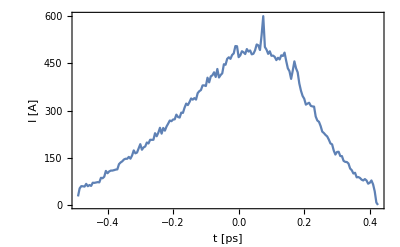

```mathematica
slicelength=0.005;
ListLinePlot[{#[[1]],Append[#[[2]],0]}//Transpose,Frame->True,PlotRange->{All,All},FrameLabel->{"t [ps]","I [A]"}]&[{1,250/(slicelength Length[#])}HistogramList[#,{slicelength}]]&[10^12(z-Mean[z])/(2.99 10^8)]
```

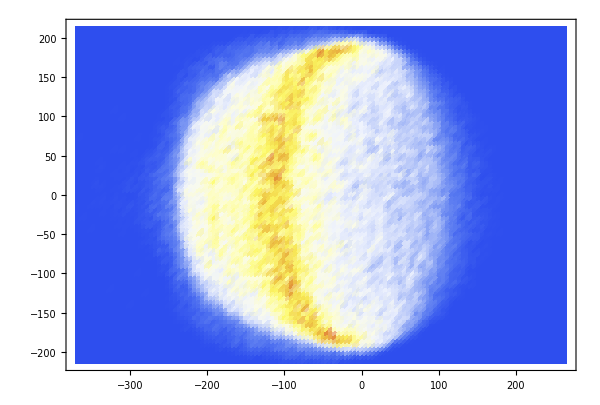

```mathematica
dplot=Block[{bins,hdata},
{bins,hdata}=HistogramList[10^6 Transpose[{x,y}],{100,100}];
ListDensityPlot[Transpose[hdata],AspectRatio->Automatic,ImageSize->600,DataRange->({#[[1]],#[[-1]]}&/@bins),Mesh->None,ColorFunction->(ColorData["TemperatureMap"])]]
```